# MultiLinearMaps

The basic idea of the package is to provide semantics for multilinear maps, so that give names to systems, associate matrices or tensors to maps between various input and output vector spaces, and then let the computer work out precisely how to compose the two maps. Developed for use in performing calculations in quantum information theory.

```mathematica
<<(NotebookDirectory[EvaluationNotebook[]]<>"MultiLinearMaps.m")
$MLMVersion
```

0.3

## Quick example: Teleportation

Let’s jump in with a simple example of teleportation. First we define the three systems involved. This is done using “System”. The first entry is the name of the system (should be a string, definitely distinct from all other system names), and the second is its dimension, i.e. an integer.

```mathematica
?System
```

System[name,dimension] represents a named vector space of given dimension.

```mathematica
A=System["A",2];
B1=System["B1",2];
B2=System["B2",2];
```

The canonical (unnormalized) maximally entangled state Omega, as a ket, bra, or projection operator, is a built-in function.

```mathematica
?OmegaKet
?OmegaBra
?OmegaOp
```

OmegaKet[sys1,sys2] returns the ket corresponding to the unnormalized maximally entangled state of systems sys1 and sys2.

OmegaKet[sys1,sys2] returns the bra corresponding to the unnormalized maximally entangled state of systems sys1 and sys2.

OmegaOp[sys1,sys2] returns the projector onto the canonical maximally entangled state of systems sys1 and sys2.

So consider the case when the Bell measurement result corresponds to the projection onto Omega, in which case we’re interested in _(A B_1)⟨Ω|Ω⟩_(B_1 B_2). This is just the composition of the ket map with a bra map, which is done using ** (the Mathematica function NonCommutativeMultiply), and we have

```mathematica
testTeleport=OmegaBra[A,B1]**OmegaKet[B2,B1];
```

```mathematica
testTeleport//SystemMap
```

MapDict[{B2},{A}]

It should be equal to the identity map from A to B2:

```mathematica
?IdentityOp
```

IdentityOp[syslist] returns the identity operator on the systems in syslist.
IdentityOp[outlist,inlist] gives the identity operator from the inlist to the outlist systems. Note that the latter map is basis dependent and uses the standard basis.

```mathematica
testTeleport==IdentityOp[{B2},{A}]
```

True

We can easily mock up the whole protocol. First define the measurement bras and the correction operators. We use FromMatrix to create arbitrary maps given a matrix representation.

```mathematica
?FromMatrix
```

FromMatrix[out,in,m] returns a MultiMap object which maps the systems in the list in to those in out according to the matrix m. If only one list of systems is given, the map takes these systems to themselves.

```mathematica
Bell[j_]:=(1/Sqrt[2]OmegaBra[A,B1])**FromMatrix[{B1},Inverse@PauliMatrix[j]];
Pauli[j_]:=FromMatrix[{B2},PauliMatrix[j]];
```

We can input an arbitrary ket as a column vector using FromMatrix. The first two arguments of this function are lists of the output and input spaces, respectively, so for a ket we just input an empty list as the second argument. Additionally, we input the ket as a matrix, i.e. a column vector. Similarly, bras are specified using row vectors. To extract the matrix associated with a map, use ToMatrix (and here MatrixForm for a nice output format).

```mathematica
psi=FromMatrix[{A},{},Transpose[{{α,β}}]];
psi//ToMatrix//MatrixForm
```

(α
β)

```mathematica
?ToMatrix
```

ToMatrix[M,sortinglist] returns the matrix representation of M, with tensor subsystems ordered according to sortinglist.

Then we combine everything together for the whole teleportation protocol.

```mathematica
teleportationOutput=Sum[Pauli[j]**Bell[j]**(1/Sqrt[2]OmegaKet[B1,B2])**psi,{j,0,3}];
```

To check that it worked, we again use ToMatrix:

```mathematica
MatrixForm@ToMatrix[teleportationOutput]
```

(α
β)

## Long example: Error-correction of amplitude damping

Now an example involving quantum error-correcting codes. Our goal here is to compute the action of the amplitude damping channel on the codewords of the Bacon-Shor code, in both X and Z gauge. First we define the systems we’ll be using, as well as some simple gates. There are nine qubits involved in this code, and we’ll call the channel outputs b[1] through b[9] and the inputs e[1] through e[9].

```mathematica
KP=KroneckerProduct;
Clear[a,b,e];
b[j_]:=b[j]=System["b["<>ToString[j]<>"]",2];
e[j_]:=e[j]=System["e["<>ToString[j]<>"]",2];
a=System["a",2];
```

```mathematica
Had[sys_]:=FromMatrix[{sys},SparseArray@HadamardMatrix[2]];
CNot[ctrl_,targ_]:=FromMatrix[{ctrl,targ},SparseArray[{{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}}]];
bcn[i_,j_]:=CNot[b[i],b[j]];
h[j_]:=Had[b[j]];
```

Now we can construct the encoding circuits for X and Z gauge. Actually the following operators are their inverses, which we will make use of later. Observe that when lots of systems come into play, it’s faster to use the ComposeMaps function rather than the overloaded ** operation. Moreover, there are two built-in methods for performing the composition, one based on Dot (the default) and one based on TensorContract. In this case, Dot is faster.

```mathematica
Timing[VX=ComposeMaps[h[6],h[5],h[4],h[3],h[2],h[1],bcn[9,8],bcn[9,7],bcn[3,9],bcn[6,9],bcn[2,8],bcn[5,8],bcn[1,7],bcn[4,7]];]
Timing[VXnc=h[6]**h[5]**h[4]**h[3]**h[2]**h[1]**bcn[9,8]**bcn[9,7]**bcn[3,9]**bcn[6,9]**bcn[2,8]**bcn[5,8]**bcn[1,7]**bcn[4,7];]
Timing[VXtc=ComposeMaps[h[6],h[5],h[4],h[3],h[2],h[1],bcn[9,8],bcn[9,7],bcn[3,9],bcn[6,9],bcn[2,8],bcn[5,8],bcn[1,7],bcn[4,7],Method->"TensorContract"];]
Timing[VZ=ComposeMaps[h[3],h[6],bcn[6,9],bcn[3,9],bcn[3,2],bcn[3,1],bcn[6,5],bcn[6,4],bcn[9,8],bcn[9,7]];]
```

{0.027409,Null}

{0.123582,Null}

{0.052567,Null}

{0.007922,Null}

```mathematica
VX==VXnc
VX==VXtc
```

True

True

Ok, now we actually construct the codewords. We’ll entangle the codewords with another system, a, so that we don’t have to specify a particular linear combination of codewords. Later, if we build a decoding circuit, this would also allow us to determine the effective channel from the input to the output by using the Choi representation.

```mathematica
UX=FromMatrix[Array[e,9],ToMatrix[Adjoint[VX]]];Timing[psiX0=UX**ComposeMaps@@Array[BasisKet[e[#],0]&,8]**OmegaKet[e[9],a];]
Timing[rhoX[0]=ComposeMaps[psiX0,Adjoint[psiX0]];]
UZ=FromMatrix[Array[e,9],ToMatrix[Adjoint[VZ]]];
Timing[psiZ0=UZ**ComposeMaps@@Array[BasisKet[e[#],0]&,8]**OmegaKet[e[9],a];]
Timing[rhoZ[0]=ComposeMaps[psiZ0,Adjoint[psiZ0]];]
```

{0.019847,Null}

{0.003196,Null}

{0.007315,Null}

{0.001062,Null}

Now we construct the channel action. We’ll use the Jamiolkowski representation, so that the channel action on a state of the e systems is given by multiplication with the Jamiolkowski operator, a map from the e and b systems to themselves, followed by tracing out the e systems. (This is just the partial transpose of the Choi operator.) We’ll try leaving the damping parameter p as a variable, rather than fixing a particular value.

```mathematica
ADJ[out_System,in_System]:=FromMatrix[{out,in},SparseArray[{{1,0,0,0},{0,p,Sqrt[1-p],0},{0,Sqrt[1-p],0,0},{0,0,0,1-p}}]];
```

We could naively build up the Jamiolkowski operator for the entire channel, like so:

```mathematica
AD[n_]:=AD[n]=ComposeMaps@@Array[ADJ[b[#],e[#]]&,{n}];
```

But then one has to perform the partial trace contraction on a very large tensor. Here we just do the first five systems:

```mathematica
Timing[rhotemp=PartialTrace[ComposeMaps[AD[5],rhoX[0],Method->"Dot"],Array[e,5],Method->"TensorContract"];]
```

{7.25701,Null}

It’s much faster to perform the partial trace operations system by system, to keep the tensors involved as small as possible. In this case we can compute the entire channel action in less time that the previous method needed to compute just the first five.

```mathematica
sigmaX[0]=rhoX[0];Timing[For[i=1,i≤9,i++,sigmaX[i]=PartialTrace[ComposeMaps[ADJ[b[i],e[i]],sigmaX[i-1],Method->"Dot"],e[i],Method->"TensorContract"];]]
rhoX[1]=sigmaX[9];
```

{4.77153,Null}

In Z gauge this is less of an issue, since the input state is extremely sparse.

```mathematica
Timing[rhotemp=PartialTrace[ComposeMaps[AD[6],rhoZ[0],Method->"Dot"],Array[e,6],Method->"TensorContract"];]
sigmaZ[0]=rhoZ[0];Timing[For[i=1,i≤9,i++,sigmaZ[i]=PartialTrace[ComposeMaps[ADJ[b[i],e[i]],sigmaZ[i-1],Method->"Dot"],e[i],Method->"TensorContract"];]]
rhoZ[1]=sigmaZ[9];
```

{0.203165,Null}

{0.091418,Null}

The channel action commutes with the Pauli z operator, so the output state has no coherences between subspaces corresponding to different Z-type stabilizer operators. In other words, once we change the basis by using the decoding unitary VX or UX, the state is block diagonal in the systems corresponding to Z-type stabilizers. In Z gauge there are 6 Z-type stabilizers, so the output state can be reduced to a sequence of 64 16x16 matrices. Here we show the first 6.

{0.093286,Null}

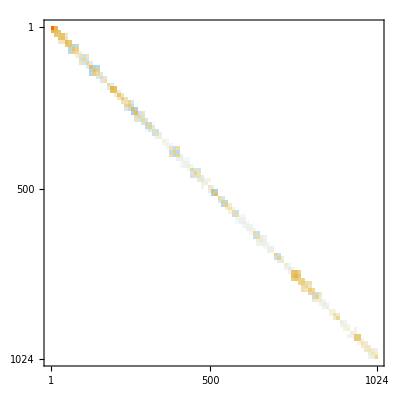

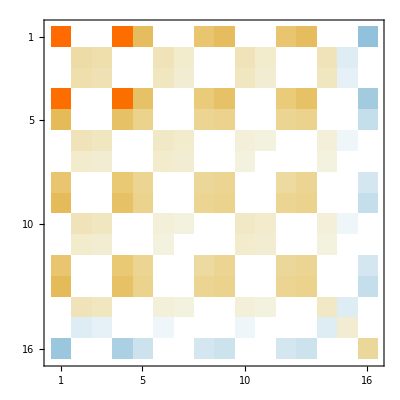
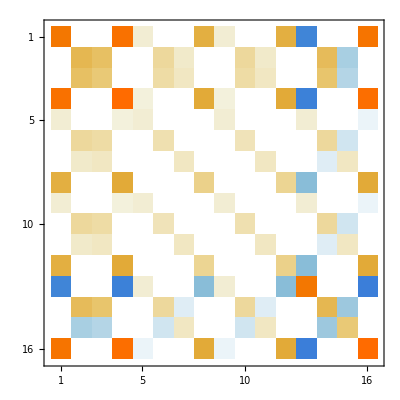
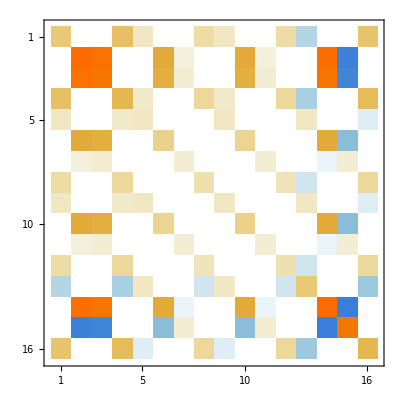
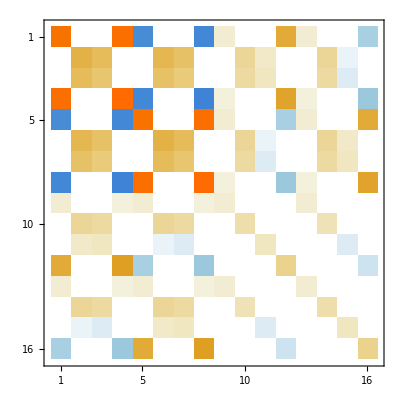
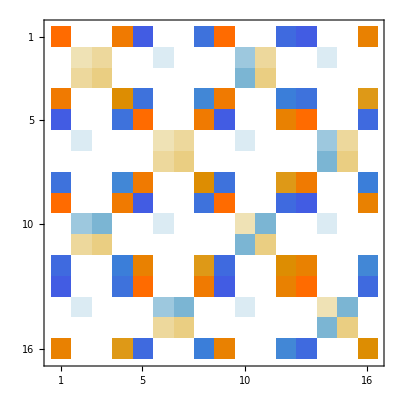
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Timing[rhoZ[2]=ComposeMaps[VZ,rhoZ[1],Adjoint[VZ],Method->"Dot"];]
rhoZn[2]=SparseArray[ArrayRules@ToMatrix[rhoZ[2],{b[1],b[2],b[4],b[5],b[7],b[8],b[3],b[6],b[9],a}]/.p->.1];
MatrixPlot[rhoZn[2]]
MatrixPlot/@(Take[Diagonal@Partition[rhoZn[2],{16,16}],6])
```

In X gauge we’re nearing the limit of what can be done symbolically in a reasonable amount of time, in particular because applying VX results in a matrix that is only 90% zeros, i.e. not terribly sparse. Instead we can input a particular value of p directly. Now there are only 2 Z-type stabilizers.

```mathematica
rhoXn[1]=MultiMap[rhoX[1][[1]],SparseArray[ArrayRules[rhoX[1][[2]]]/.p->.1]];
Timing[rhoX[2]=ComposeMaps[VX,rhoXn[1],Adjoint[VX],Method->"Dot"];]
MatrixPlot@ToMatrix[rhoX[2],{b[7],b[8],b[1],b[2],b[3],b[4],b[5],b[6],b[9],a}]
```

{0.191858,Null}

-Graphics-

## Constructors

Several basic constructors are available. Basis kets & bras, the unnormalized entangled state, the identity operator, and the swap operator. An arbitrary map can be input in matrix form using FromMatrix.

Here is a basis vector of system A. The indexing starts at zero and the function will complain if the index is out of range.

```mathematica
BasisKet[A,0]
BasisKet[A,2]
```

MultiMap[IndexDict[VecSpace[AtomicSpace[System[A,2],ket]]],SparseArray[<1>, {2}]]

BasisElement::dim: Requested element must be an integer between 0 and 1

BasisElement[System[A,2],2,ket]

The identity operator for a single system or collection of systems.

```mathematica
IdentityOp[{A,B1}]
IdentityOp[A]
```

MultiMap[IndexDict[VecSpace[AtomicSpace[System[A,2],ket],AtomicSpace[System[B1,2],ket]],VecSpace[AtomicSpace[System[A,2],bra],AtomicSpace[System[B1,2],bra]]],SparseArray[<4>, {4, 4}]]

MultiMap[IndexDict[VecSpace[AtomicSpace[System[A,2],ket]],VecSpace[AtomicSpace[System[A,2],bra]]],SparseArray[<2>, {2, 2}]]

## Composition

Composition by ** (or NonCommutativeMultiply)

```mathematica
?ComposeMaps
```

ComposeMaps[M1,M2,...,Method->method] returns the composition M1 ◦ M2 ◦ ⋯. Accessible by the infix notation M1 ** M2.
     Additionally, there are two internal methods of computing the composition, available as "Dot" and "TensorContract". The former is the default as it appears to be faster.

```mathematica
M1=FromMatrix[{A},{A,B1},RandomReal[{0,1},{2,4}]];
M2=FromMatrix[{B2},{A},RandomReal[{0,1},{2,2}]];
```

```mathematica
M1**M2
```

ComposeMaps::inputs: Input maps are not composable in this order.

MultiLinearMaps`Private`ComposeMapsDot[MultiMap[IndexDict[VecSpace[AtomicSpace[System[A,2],ket]],VecSpace[AtomicSpace[System[A,2],bra],AtomicSpace[System[B1,2],bra]]],SparseArray[<8>, {2, 4}]],MultiMap[IndexDict[VecSpace[AtomicSpace[System[B2,2],ket]],VecSpace[AtomicSpace[System[A,2],bra]]],SparseArray[<4>, {2, 2}]]]

```mathematica
ToMatrix[M2**M1]==ToMatrix[M2].ToMatrix[M1]
```

True

There are two internal methods of composing maps, one using the built-in function TensorContract and the other using Dot. The latter seems to be faster, and is the default, but both are available by specifying the method of ComposeMaps.

```mathematica
ComposeMaps[M2,M1,Method->"TensorContract"]==ComposeMaps[M2,M1,Method->"Dot"]
```

The change can be made to the infix notation as well by redefining the default:

```mathematica
Unprotect[ComposeMaps];
Options[ComposeMaps]={Method->"TensorContract"};
Protect[ComposeMaps];
```

## Contraction

```mathematica
?PartialTrace
```

PartialTrace[M,syslist,Method->method] returns the partial trace of M with respect to the systems in syslist. If no systems are explicitly given, all systems that can be traced out are. An empty list {} will return the input map.
     Additionally, there are two internal methods of computing the partial trace, available as "Dot" and "TensorContract". The former is the default as it appears to be faster in most cases.

```mathematica
rhomat=RandomReal[{0,1},{8,8}];
rhomat=rhomat.Transpose[rhomat];
rhomat=rhomat/Tr[rhomat];
rho=FromMatrix[{A,B1,B2},rhomat];
```

```mathematica
ToMatrix@PartialTrace[rho]
```

1.

```mathematica
MatrixForm@ToMatrix@PartialTrace[rho,A]
```

(0.221999 | 0.144578 | 0.211287 | 0.175042
0.144578 | 0.175734 | 0.185147 | 0.192385
0.211287 | 0.185147 | 0.293702 | 0.230366
0.175042 | 0.192385 | 0.230366 | 0.308565)

```mathematica
MatrixForm@ToMatrix@PartialTrace[rho,{A,B1}]
```

(0.515597 | 0.393342
0.393342 | 0.484403)

```mathematica
ToMatrix@PartialTrace[rho,{}]==ToMatrix@rho
```

True

```mathematica
?AddMaps
```

AddMaps[M1,M2,Method->method] returns the sum of the two maps. Accessible infix as M1 + M2.
AddMaps will moreover add compatible maps, those that can be made to represent the same kind of mapping by including suitable identity operations.
     This option, which is the default method "Lazy", can be turned off by specifying the "Strict" method

```mathematica
Unprotect[AddMaps];
Options[AddMaps]={Method->"Lazy"};
Protect[AddMaps];
```

```mathematica
?PartialTranspose
```

PartialTranspose[M,syslist] returns the partial transpose of M with respect to the systems in syslist.

```mathematica
?Adjoint
```

Adjoint[M] returns the adjoint of M.